# Calcolo della risposta al gradino unitario (discreto) per un sistema LTI-TD (partiamo dalla I/S/U)

```mathematica
ClearAll["Global`*"]
```

Inserisco la terna A, B, C

```mathematica
A={{0,1,0},{0,0,1},{1/12,1/4,-1/3}};B={{0},{0},{1}};Cc={1,1,0};
```

```mathematica
Eigenvalues[A]
```

{-1/2,1/2,-1/3}

```mathematica
A//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
1/12 | 1/4 | -1/3)

```mathematica
B//MatrixForm
```

(0
0
1)

```mathematica
Cc//MatrixForm
```

(1
1
0)

Mi calcolo la funzione di trasferimento del sistema

```mathematica
G[z_]:=Simplify[Cc.Inverse[z IdentityMatrix[3]-A].B]
```

```mathematica
G[z]
```

{(12 (1+z))/(-1-3 z+4 z^2+12 z^3)}

```mathematica
Factor[G[z]]
```

{(12 (1+z))/((-1+2 z) (1+2 z) (1+3 z))}

Mi costruisco, nel dominio z, la risposta al gradino (unitario)

```mathematica
Y[z_]:=G[z][[1]] (z/(z-1))
```

```mathematica
Y[z]
```

(12 z (1+z))/((-1+z) (-1-3 z+4 z^2+12 z^3))

```mathematica
ZTransform[UnitStep[k],k,z]
```

z/(-1+z)

Passo 1. Per determinare l’antitrasformata zeta, divido Y(z) per z

```mathematica
Y[z]/z
```

(12 (1+z))/((-1+z) (-1-3 z+4 z^2+12 z^3))

I fratti semplici di Y[z]/z saranno 4

```mathematica
Subscript[C, 1]/(z-1)+Subscript[C, 2]/(z-1/2)+Subscript[C, 3]/(z+1/2)+Subscript[C, 4]/(z+1/3);
```

```mathematica
Subscript[C, 1]=lim_(z->1) (z-1)(Y[z]/z)
```

2

```mathematica
Subscript[C, 2]=lim_(z->1/2) (z-1/2)(Y[z]/z)
```

-18/5

```mathematica
Subscript[C, 3]=lim_(z->-1/2) (z+1/2)(Y[z]/z)
```

-2

```mathematica
Subscript[C, 4]=lim_(z->-1/3) (z+1/3)(Y[z]/z)
```

18/5

```mathematica
Subscript[C, 1]/(z-1)+Subscript[C, 2]/(z-1/2)+Subscript[C, 3]/(z+1/2)+Subscript[C, 4]/(z+1/3)
```

2/(-1+z)-18/(5 (-1/2+z))+18/(5 (1/3+z))-2/(1/2+z)

Passo 2, moltiplicare per z la funzione di variabile complessa Y(z)/z

```mathematica
Subscript[C, 1] z/(z-1)+Subscript[C, 2] z/(z-1/2)+Subscript[C, 3] z/(z+1/2)+Subscript[C, 4] z/(z+1/3)
```

(2 z)/(-1+z)-(18 z)/(5 (-1/2+z))+(18 z)/(5 (1/3+z))-(2 z)/(1/2+z)

Passo 3, scrittura della risposta forzata nel dominio del tempo a partire dalle successioni elementari  che generano i fratti semplici nella forma

```mathematica
Subscript[y, f][k_]:=Subscript[C, 1] UnitStep[k]+Subscript[C, 2](1/2)^k UnitStep[k]+Subscript[C, 3](-1/2)^k UnitStep[k]+Subscript[C, 4](-1/3)^k UnitStep[k]
```

Rappresentazione grafica

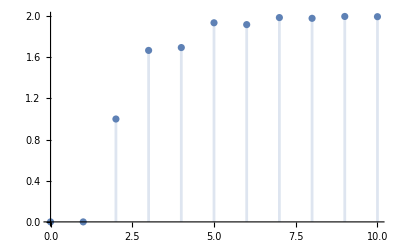

```mathematica
DiscretePlot[Subscript[y, f][k],{k,0,10},PlotRange->All]
```